```mathematica
ClearAll["Global`*"]
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
data = Import[NotebookDirectory[]<>"SpherePlaneResistance.txt","Table"];
ξdata=data[[All,1]];
XAdata=data[[All,2]];
YAdata=data[[All,3]];
YBdata=data[[All,4]];
XCdata=data[[All,5]];
YCdata=data[[All,6]];
δ=0.01;
YAVal=Interpolation[Transpose[{ξdata,YAdata}]][δ];
YBVal=Interpolation[Transpose[{ξdata,YBdata}]][δ];
YCVal=Interpolation[Transpose[{ξdata,YCdata}]][δ];
XAVal=Interpolation[Transpose[{ξdata,XAdata}]][δ];
XCVal=Interpolation[Transpose[{ξdata,XCdata}]][δ];
AA={{YAVal,0,0},{0,YAVal,0},{0,0,XAVal}};
BB={{0,YBVal,0},{-YBVal,0,0},{0,0,0}};
CC={{YCVal,0,0},{0,YCVal,0},{0,0,XCVal}};
Resistance=ArrayFlatten[ {{AA,Transpose[BB]},{BB,CC}}];
```

```mathematica
TrigReduce[Cos[0.3 t] Sin[0.03 t]]
```

1/2 (-Sin[(0.27+0. ⅈ) t]+Sin[(0.33+0. ⅈ) t])

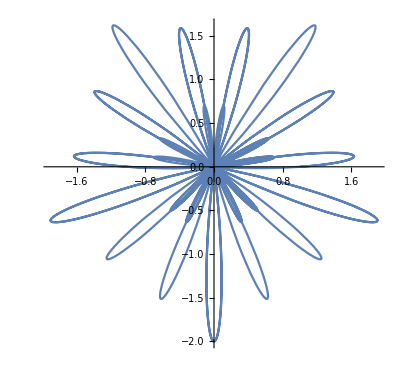

```mathematica
ParametricPlot[{(Cos[0.2 t ]+Sin[0.3 t]) Cos[0.02t],(Cos[0.2 t ]+Sin[0.3 t]) Sin[0.02 t] },{t,0,500}]
```

```mathematica
B[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]:={B1 Cos[(ω1-ω4)t]+B2 Cos[(ω1+ω4) t],-B1 Sin[(ω1-ω4) t]+B2 Sin[(ω1+ω4) t], (A1 Sin[t ω1 ]+A2*Sin[ω2 t ]+A3 Sin[ω3 t])}.RotationMatrix[10 Degree ,{0,1,0}];

Bflat[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]:={B1 Cos[(ω1-ω4)t]+B2 Cos[(ω1+ω4) t],-B1 Sin[(ω1-ω4) t]+B2 Sin[(ω1+ω4) t], (A1 Sin[t ω1 ]+A2*Sin[ω2 t ]+A3 Sin[ω3 t])};
```

```mathematica
B[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]:={(B1 Cos[t ω1 ]+B2*Cos[ω2 t ])*Sin[ω4 t],(B1 Cos[t ω1 ]+B2*Cos[ω2 t ])*Cos[ω4 t], (A1 Sin[t ω1 ]+A2*Sin[ω2 t ]+A3 Sin[ω3 t])}.RotationMatrix[10 Degree ,{0,1,0}];

Bflat[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]:={(B1 Cos[t ω1 ]+B2*Cos[ω2 t ])*Sin[ω4 t],(B1 Cos[t ω1 ]+B2*Cos[ω2 t ])*Cos[ω4 t],(A1 Sin[t ω1 ]+A2*Sin[ω2 t ]+A3 Sin[ω3 t])};
```

```mathematica
roller[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_}]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data,dct,tdata},
parameter={ω1,ω2,ω3,ω4,A1,A2,A3,B1,B2};
tMax = (*Min[200 2 π/parameter[[1]],50000.0]*0+*)5000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,B[parameter,t    ]   ]];
(*force *)
F ={0 ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*data=Table[x[t]/.sol[[1]],{t,0,4000,1}];
dct=FourierDCT[data];
  tdata=FourierDCT[PadRight[Take[dct,2],4000,0],3];*)
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
(*data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}*)
sol
]
rollerflat[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_}]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data,dct,tdata},
parameter={ω1,ω2,ω3,ω4,A1,A2,A3,B1,B2};
tMax =(* Min[200 2 π/parameter[[1]],50000.0]+*)5000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,Bflat[parameter,t    ]   ]];
(*force *)
F ={0 ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*data=Table[x[t]/.sol[[1]],{t,0,4000,1}];
dct=FourierDCT[data];
  tdata=FourierDCT[PadRight[Take[dct,2],4000,0],3];*)
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
(*data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}*)
sol
]


(*B[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]*)
```

```mathematica
(*ω1=0.3;
ω2=0.3 2;
ω3=0.3*3;
ω4=0.01;
A1=1/10 4;
A2=-1/10 0;
A3=1/15 0;
B1=0.5;
B2=0.8;*)
can={};
For [i=0,i<1000,
ω1=RandomReal[{0.2,0.4}];
ω2=RandomReal[{ω1,1}];
ω3=RandomReal[{ω2,2}];
ω4=ω1/RandomReal[{10,30}];
A1=RandomReal[{-2,2}];
A2=RandomReal[{-2,2}];
A3=RandomReal[{-2,2}];
B1=RandomReal[{-2,2}];
B2=RandomReal[{-2,2}];
sol1=roller[{ω1,ω2,ω3,ω4,A1,A2,A3,B1, B2}];
sol2=rollerflat[{ω1,ω2,ω3,ω4,A1,A2,A3,B1, B2}];
bias=Table[x[t]/.sol1[[1]],{t,1,5000}];
flat=Table[x[t]/.sol2[[1]],{t,1,5000}];
If[(Min[flat]-Min[bias]>2)&&(Abs[Min[bias]/(y[t]/.sol1[[1]]/.t->Ordering[bias,1][[1]])]>1), can =Append[can,{ω1,ω2,ω3,ω4,A1,A2,A3,B1, B2}]];
i++
]
```

```mathematica
Tan[45 Degree] 1.0
```

1.

```mathematica
Length[can]
```

20

12.8481

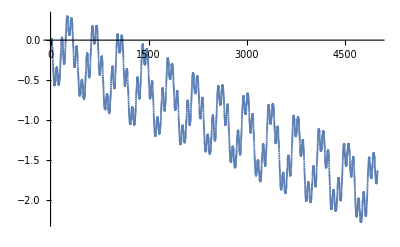

```mathematica
ListPlot[flat]
```

```mathematica
Length[can]
```

24

```mathematica
can
```

{{0.293671,0.928833,1.36989,0.0182316,-0.302568,-0.394213,1.16394,1.93121,-1.93735},{0.235847,0.679004,1.21004,0.0118003,-0.031716,1.84566,-0.0384447,-0.488093,1.23802},{0.336201,0.978477,1.3362,0.0191559,-0.0525849,1.58048,-1.38268,1.83294,-0.411568},{0.263296,0.872671,1.06102,0.0108202,0.294614,-1.28693,-0.606592,1.90619,1.69244},{0.395538,0.811714,1.74545,0.0163775,-0.734322,-1.06261,-1.269,-1.0565,1.91074},{0.350795,0.728892,1.20102,0.0285766,-1.31189,1.4772,-0.144453,-0.697497,-0.157244},{0.238288,0.590466,0.983113,0.0096145,-0.622678,-0.668707,1.61807,-1.83483,1.9595},{0.231668,0.675994,1.55961,0.00871234,0.0012971,1.69128,0.827907,1.0671,-1.8627},{0.368901,0.866217,1.19057,0.0343028,-1.33695,-1.85954,-0.859472,1.37682,-1.3904},{0.30916,0.482488,0.927366,0.028973,0.498585,0.0846948,-1.67491,0.737835,-0.949997},{0.213219,0.612661,0.970479,0.0124788,0.433087,-1.59101,-0.880524,-0.0655804,1.27435},{0.394932,0.776578,1.92785,0.0154276,1.54876,-0.231874,-0.00716175,-0.203189,0.804617},{0.364466,0.833688,1.61961,0.0216531,0.75005,1.69043,-1.37216,1.75401,-1.47148},{0.292444,0.815923,1.07771,0.0252185,0.900401,1.42382,-1.84711,1.40436,-1.63191},{0.363183,0.789093,1.44334,0.0191353,0.285058,-0.712914,-1.39778,1.61031,0.651441},{0.391231,0.840977,1.48421,0.0380907,-0.551688,-0.971819,-1.74313,-1.31133,1.32678},{0.287708,0.824454,1.17494,0.0248913,0.376015,-1.01137,-0.781249,1.90797,1.36304},{0.279306,0.749698,1.18066,0.0110949,0.462625,-0.0601438,-1.73595,-1.91128,1.68833},{0.379384,0.96556,1.3161,0.0255447,-0.40409,-0.898129,0.842032,-0.599411,-1.9896},{0.288771,0.75396,1.06044,0.0103633,0.438365,-1.8783,0.107133,-0.67283,-1.78734},{0.258374,0.988195,1.14994,0.0251884,-0.239016,1.67346,-0.137384,-1.42481,-0.961923},{0.22042,0.617145,1.66799,0.0094825,-1.0446,1.58825,1.22501,1.34291,1.94784},{0.269318,0.712518,1.07377,0.0102226,-0.508008,-1.414,0.613738,-1.61266,1.78825},{0.279975,0.666047,1.82617,0.0134816,-0.436145,0.966283,-1.91,1.51178,0.785447},{0.218675,0.691997,1.69004,0.0102152,0.118997,1.32841,-0.234118,-1.26068,0.148924},{0.220527,0.842336,1.15544,0.0143425,-0.512506,0.819488,-1.32533,-1.26537,-1.98684},{0.311295,0.937246,1.98826,0.0209983,-0.39726,-1.50041,0.993949,1.4434,-1.79663},{0.20873,0.571928,1.37527,0.0112543,0.68168,1.43451,0.275693,-1.88883,0.941968},{0.288046,0.436158,1.88023,0.0141931,-0.770605,1.17464,-0.676222,-1.02697,-1.7338},{0.306407,0.758886,1.38806,0.0216427,0.518666,1.83456,0.988313,-0.442631,1.96268},{0.289495,0.752616,1.52943,0.015229,0.0574845,1.75685,-0.116703,0.382988,1.66492},{0.323843,0.587608,1.50542,0.0198565,-0.096998,-0.467885,0.665448,0.926996,-0.383765},{0.376516,0.607737,0.872875,0.0207097,-1.90392,-1.05482,1.55523,-0.402161,-0.16054},{0.36022,0.959045,1.04842,0.0124739,0.587153,-1.51739,-0.437418,-0.4081,0.823127},{0.335649,0.800122,1.93333,0.0200208,-1.30944,-1.94237,-1.74137,1.84232,-1.8721},{0.393118,0.738545,1.07048,0.0188922,0.795924,-0.495196,0.226148,-0.790945,0.413678},{0.228726,0.604359,1.70439,0.0132404,-0.590008,1.69083,-0.324894,1.23522,1.65314}}

{s,s}

```mathematica
Export["can.csv",can]
```

can.csv

```mathematica
{0.22330750556920723,0.8643009735502367,1.8595145024685116,0.007884037066915416,0.5488351722004445,1.4713052459131095,-0.718568322512021,1.9621859943316782,-1.224792308422301}
{0.2477745963909214,0.6612842912088941,1.8357372323735794,0.017283236066773556,-0.03405976406370126,1.7463380230395433,0.11593836637793853,-0.7499406232559771,1.6651813719458097}
{0.26609327792084664,0.641772514040313,1.7930721767342677,0.012675283731216475,-1.1363480596577622,1.981379071098937,0.28557464294617674,1.285838747599822,1.696533416996953}
```

Part::partw: Part 25 of {{0.303199,0.723896,0.906524,0.018328,-0.089091,1.88875,1.07472,-1.03514,0.109033},{0.248379,0.788075,0.829196,0.0235706,1.06289,1.89516,-0.159703,1.3963,-1.97747},«21»,{0.379727,0.987886,1.14161,0.020117,0.278775,-0.936106,-1.23465,-1.93987,-0.279906}} does not exist.

ReplaceAll::reps: {{{0.303199,0.723896,0.906524,0.018328,-0.089091,1.88875,1.07472,-1.03514,0.109033},{0.248379,0.788075,0.829196,0.0235706,1.06289,1.89516,-0.159703,1.3963,-1.97747},«21»,{0.379727,0.987886,1.14161,0.020117,0.278775,-0.936106,-1.23465,-1.93987,-0.279906}}⟦25⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

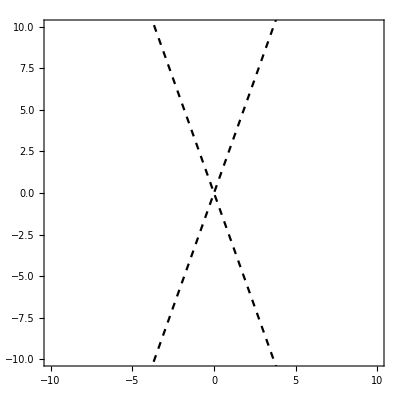

```mathematica
para=can[[25]]
sol1=roller[para];
sol2=rollerflat[para];
Show[
ParametricPlot[{x[t]/.sol1[[1]],y[t]/.sol1[[1]]},{t,0,5000},PlotStyle->{Red, AbsoluteThickness[0.9]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False],
ParametricPlot[{x[t]/.sol2[[1]],y[t]/.sol2[[1]]},{t,0,5000},PlotStyle->{Blue, AbsoluteThickness[0.9]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False],
Plot[{Cot[20 Degree]x,-Cot[20 Degree]x},{x,-10,10},PlotStyle->{{Dashed,Black},{Dashed,Black}}]

]
```

```mathematica
Pick[can[[2]],{1,1,1,0,1,1,1,0,0},1]
```

{0.114839,0.547198,0.704085,-0.317738,0.0414221,0.144293}

```mathematica
can[[2]][[1;;3]]
```

{0.114839,0.547198,0.704085}

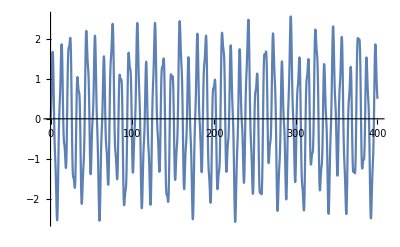

```mathematica
zfield[{ω1_,ω2_,ω3_,A1_,A2_,A3_},t_]:=A1 Sin[ω1 t ]+A2 Sin[ω2 t ]+A3 Sin[ω3 t ]
Plot[zfield[Pick[can[[37]],{1,1,1,0,1,1,1,0,0},1],t],{t,0,400}]
```